```mathematica
analyzeRectification[file_, avgStartTime_:70] := Module[{data, dataToAvg, avg, stddev},
SetDirectory[NotebookDirectory[]];
data = Check[Import[file, "Table"], Return["Unable to import file"]];
dataToAvg = Select[data, #1[[1]]>avgStartTime&];
avg = Mean[#1[[2]]&/@dataToAvg];
stddev = Sqrt[Mean[#1[[2]]^2&/@dataToAvg]-avg^2];
Print[
Show[
Graphics[{Pink, Rectangle[{avgStartTime, 0}, {data[[-1, 1]], 1}]}],
ListPlot[data], 
AspectRatio->.5,
PlotRange->{0, 1}, Frame->True, LabelStyle->15, FrameLabel->{{"Rectification",None}, {"Time",None}}, ImageSize->400]];
"Mean rectification = " <>ToString[avg] 
  "\nStandard error  = "<>ToString[stddev]
];
```

```mathematica
To calculate the degree of rectification from simulation output, insert 
the filename below and evaluate.  The output shows the amount of rectification 
over time, with the colored rectangle marking the region that will be averaged 
over.  The width of this region can be adjusted by passing a second argument 
denoting the time at which to start averaging 
(e.g. analyzeRectification["file.txt", 60]).
```

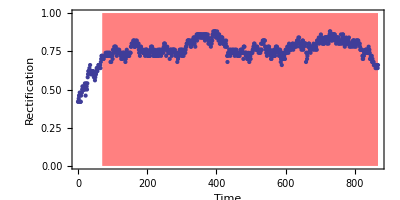

Mean rectification = 0.772346 
Standard error  = 0.0476198

```mathematica
analyzeRectification["rectification_Dr[0.2]_ws[4].out"]
```